# MATH7501, Prac 1, Sem 1-2021

## Basic Mathematica Usage

## Section 1: Entering Calculations

### 1.1: Free-Form Input

WolframAlphaQueryParseResults

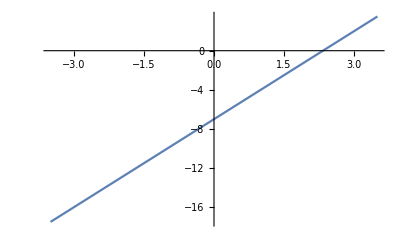

### 1.2: wolfram Language

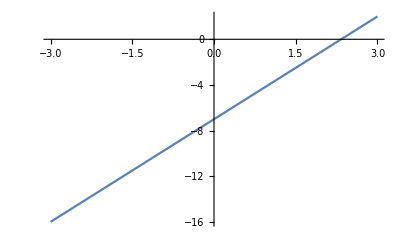

```mathematica
Plot[{3x-7},{x,-3,3}]
```

```mathematica
Plot[{3x-7},{x,-3,3}];
```

```mathematica
? Plot
```

### 1.3: Palette

```mathematica
Plot[{y = 3x - 7},{x,-3,3}]
```

-Graphics-

```mathematica
N[1/(√(2×π))]
```

0.398942

```mathematica
a = 3;
3a+1
```

10

```mathematica
Clear [a]
```

```mathematica
3a + 1 /.a->3
```

10

```mathematica
Integrate[Sin[2x],x]
```

-1/2 Cos[2 x]

```mathematica
Integrate[Cos[2x],x]
```

1/2 Sin[2 x]

```mathematica
Simplify[1/2 Sin[2 x]]
```

Cos[x] Sin[x]

```mathematica
Solve[3x+12==0,x]
```

{{x→-4}}

```mathematica
SumOfSquares[x_,y_]:= x^2+ y^2;
SumOfSquares[2,3]
```

13

```mathematica
SumOfNumbers[n_]:= Module[{k}, Sum[k,{k,1,n}]];
SumOfNumbers[5]
```

15

```mathematica
SumOfNSquares[n_]:= Module[{k}, Sum[k^2,{k,1,n}]];
SumOfNSquares[5]
```

55